```mathematica
Quit[]
```

## Load data

```mathematica
(* Load data first *)
Do[
cohomology[NN]=Import[NotebookDirectory[]<>"cohomology_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
MaxLevel[NN_] := Switch[NN,
2,25,
3,19,
4,15];
NumAllStatesUpToLevel[NN_,level_] := Total[#[[9]]&/@Select[cohomology[NN],#[[1]]<=level&]];
NumAllStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,9]];
NumMultiGravitonStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,10]];
```

```mathematica
(* Usage example *)
NumAllStates[2,{0,0,4,4,4},7]
NumMultiGravitonStates[2,{0,0,4,4,4},7]
```

1

0

## U(1) partition function

```mathematica
level=25;
ZU1sw[x_,a_,b_,u_,v_,w_]:=(a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b)) x
ZU1B[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]+ZU1sw[-x,a,b,-u,-v,-w])
ZU1F[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]-ZU1sw[-x,a,b,-u,-v,-w])

ZU1[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(ZU1B[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n ZU1F[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
ZU1reduced[x_]:=ZU1[1,x^3,x^3,x^2,x^2,x^2]
IU1reduced[x_]:=ZU1[-1,x^3,x^3,-x^2,-x^2,-x^2]
```

## Partition function

```mathematica
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
PermutationMultiplicity[charges_] := Length[Permutations[charges[[1;;2]]]]*Length[Permutations[charges[[3;;5]]]];
Index[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[3;;5]]) PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
NumAllStates[NN_,charges_] := Sum[ PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
Index[NN_,level_] := Sum[Index[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
NumAllStates[NN_,level_] := Sum[NumAllStates[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
Index[NN_] := Index[NN] = Series[(1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
NumAllStates[NN_] :=NumAllStates[NN] = Series[(1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UIndex[NN_] := UIndex[NN] = Series[IU1reduced[x] (1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UNumAllStates[NN_] := UNumAllStates[NN] = Series[ZU1reduced[x] (1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

```mathematica
UIndex[2]
```

1+3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+O[x]^26

```mathematica
Index[2]
```

1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25+O[x]^26

## Graviton partition function

```mathematica
level=25;
f[x_,a_,b_,u_,v_,w_]:=(1+ u)(1+ v)(1+  w)/(1-a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- u(1+ v)(1+ w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- v(1+  w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x v)/(1-x w)-1)-w/(1- a)/(1- b)((1+ x a)(1+x b)/(1-x w)-1)-a b x/(1- a)/(1- b)-((a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b))) x

fB[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]+f[-x,a,b,-u,-v,-w])/2
fF[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]-f[-x,a,b,-u,-v,-w])/2
Zgrav[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(fB[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n fF[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
Zgravreduced[x_]:=Zgrav[1,x^3,x^3,x^2,x^2,x^2]
Igravreduced[x_]:=Zgrav[-1,x^3,x^3,-x^2,-x^2,-x^2]

ZUgravreduced[x_]:=Series[ZU1reduced[x]Zgravreduced[x],{x,0,level}]
IUgravreduced[x_]:=Series[IU1reduced[x]Igravreduced[x],{x,0,level}]
```

```mathematica
ZUgravreduced[x]
IUgravreduced[x]
```

1+3 x^2+2 x^3+15 x^4+18 x^5+61 x^6+102 x^7+264 x^8+490 x^9+1107 x^10+2160 x^11+4574 x^12+9018 x^13+18375 x^14+36160 x^15+71931 x^16+140406 x^17+274534 x^18+530754 x^19+1023942 x^20+1960192 x^21+3739383 x^22+7091604 x^23+13396454 x^24+25183602 x^25+O[x]^26

1+3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+48 x^8-42 x^9+99 x^10-96 x^11+200 x^12-198 x^13+381 x^14-396 x^15+711 x^16-750 x^17+1278 x^18-1386 x^19+2256 x^20-2472 x^21+3879 x^22-4320 x^23+6564 x^24-7362 x^25+O[x]^26

## Tables

```mathematica
NN = 2;
StringReplace[Join[{{"Level","SU","SU Index","U", "U Index"}},Join[{Range[0,MaxLevel[NN]]},CoefficientList[{NumAllStates[NN],Index[NN],UNumAllStates[NN],UIndex[NN]},x]]//Transpose]//MatrixForm//TeXForm//ToString,{"\\\\"->"\\\\\\hline"}]
```

\left(
\begin{array}{ccccc}
 \text{Level} & \text{SU} & \text{SU Index} & \text{U} & \text{U Index} \\\hline
 0 & 1 & 1 & 1 & 1 \\\hline
 1 & 0 & 0 & 0 & 0 \\\hline
 2 & 0 & 0 & 3 & 3 \\\hline
 3 & 0 & 0 & 2 & -2 \\\hline
 4 & 6 & 6 & 15 & 9 \\\hline
 5 & 6 & -6 & 18 & -6 \\\hline
 6 & 9 & -7 & 51 & 11 \\\hline
 7 & 18 & 18 & 90 & -6 \\\hline
 8 & 30 & 6 & 195 & 9 \\\hline
 9 & 40 & -36 & 362 & 14 \\\hline
 10 & 66 & 6 & 699 & -21 \\\hline
 11 & 120 & 84 & 1308 & 36 \\\hline
 12 & 198 & -80 & 2431 & -17 \\\hline
 13 & 324 & -132 & 4434 & -18 \\\hline
 14 & 537 & 309 & 8046 & 114 \\\hline
 15 & 822 & -18 & 14346 & -194 \\\hline
 16 & 1257 & -567 & 25434 & 258 \\\hline
 17 & 1944 & 516 & 44544 & -168 \\\hline
 18 & 2959 & 613 & 77442 & -112 \\\hline
 19 & 4476 & -1392 & 133386 & 630 \\\hline
 20 & 6834 & -180 & 228021 & -1089 \\\hline
 21 & 10352 & 2884 & 386898 & 1130 \\\hline
 22 & 15540 & -1926 & 651843 & -273 \\\hline
 23 & 23406 & -4242 & 1091004 & -1632 \\\hline
 24 & 35076 & 7890 & 1814578 & 4104 \\\hline
 25 & 52020 & 792 & 2999724 & -5364 \\\hline
\end{array}
\right)

## Plots

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 1.5;
```

```mathematica
Do[
Export["/Users/yinhslin/git/bh/SU"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[NumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[Index[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["SU("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}},TicksStyle->Directive[Black,size]]];
Export["/Users/yinhslin/git/bh/U"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[UNumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[UIndex[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["U("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}}]];
,{NN,2,4}
]
```

## Load anomalous dimensions

```mathematica
(* Load data first *)
Do[
ad[NN]=Import[NotebookDirectory[]<>"ad_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
```

```mathematica
MaxLevel[NN_] := Switch[NN,
2,24,
3,17,
4,15];
OrganizeData[data_]:=Tally[Sort[Flatten[#[[9;;]]&/@data]]];
AD[NN_]:=ad[NN]//OrganizeData;
AD[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]//OrganizeData];
AD[NN_,charges_,degree_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&&#[[7]]==degree&]//OrganizeData];
ADUpToLevel[NN_,level_]:=Select[ad[NN],#[[1]]<=level&]//OrganizeData;
```

## Partition function

```mathematica
charges[level_]:=Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]]
```

```mathematica
charges[4]
```

{{0,0,0,0,2},{0,0,0,1,1}}

```mathematica
Table[ed,{l,4,12},{c,charges[l]},{d,2,Total[c]},{ed,AD[2,c,d]}]
```

{{{{{0,1}}},{{{0,1}}}},{{{{0,1}}}},{{{},{}},{{{0,1}},{}},{{{0,2},{1.5,1}},{{1.5,1}}},{{}},{{{0,1}}}},{{{{0,1}},{}},{{{0,2},{1.5,1}},{{1.5,1}}}},{{{},{},{{0,1}}},{{},{},{{0,1}}},{{},{{1.5,1}},{{0,1},{1.5,1}}},{{{0,1},{1.5,1}},{{1.5,2}},{{0,1},{1.5,1}}},{{{0,1},{1.5,1}},{{1.5,1}}},{{{0,2},{1.5,1}},{{1.5,1}}}},{{{},{},{{0,1}}},{{{0,1},{1.5,1}},{{1.5,2}},{{0,1},{1.5,1}}},{{{0,3},{1.5,4}},{{1.5,6}},{{0,1},{1.5,2}}},{{{1.5,1}},{{1.5,1}}},{{{0,1},{1.5,1}},{{1.5,1}}}},{{{},{},{},{}},{{},{},{{0,1}},{}},{{},{{1.5,1}},{{0,1},{1.5,1}},{}},{{},{{1.5,1}},{{0,3},{1.5,1},{2.5,1}},{{2.5,1}}},{{{1.5,1}},{{1.5,4}},{{0,3},{1.5,3},{2.5,1}},{{2.5,1}}},{{{0,1},{1.5,1}},{{1.5,1}},{}},{{{0,2},{1.5,3}},{{1.5,4}},{{1.5,1}}},{{{0,1},{1.5,1}},{{1.5,2}},{{0,1},{1.5,1}}},{{{0,3},{1.5,4}},{{1.5,6}},{{0,1},{1.5,2}}}},{{{},{},{{0,1}},{}},{{},{{1.5,1}},{{0,3},{1.5,1},{2.5,1}},{{2.5,1}}},{{{1.5,1}},{{1.5,4}},{{0,3},{1.5,3},{2.5,1}},{{2.5,1}}},{{{0,1},{1.5,3}},{{1.5,8},{1.875,1}},{{0,6},{1.5,5},{1.875,1},{2.5,3}},{{2.5,3}}},{{{0,1},{1.5,2}},{{1.5,2}},{}},{{{0,2},{1.5,3}},{{1.5,4}},{{1.5,1}}}},{{{},{},{},{},{{0,1}}},{{},{},{},{},{{0,1}}},{{},{},{},{{2.5,1}},{{0,1},{2.5,1}}},{{},{{1.5,1}},{{1.5,1}},{{2.5,1}},{{0,1},{2.5,1}}},{{},{},{{0,2},{2.5,1}},{{2.5,2}},{{0,1},{2.5,1}}},{{},{{1.5,2}},{{0,3},{1.5,2},{1.875,1},{2.5,2}},{{1.875,1},{2.5,4}},{{0,1},{2.5,2}}},{{{1.5,1}},{{1.5,4}},{{0,4},{1.5,3},{1.875,2},{2.5,3}},{{1.875,2},{2.5,6},{4.5,1}},{{0,1},{2.5,3},{4.5,1}}},{{},{},{{0,2},{2.5,1}},{{2.5,1}}},{{{0,1},{1.5,2}},{{1.5,4},{1.875,1}},{{0,3},{1.5,2},{1.875,1},{2.5,2}},{{2.5,2}}},{{{0,3},{1.5,7},{2.08333,1}},{{1.5,12},{1.875,3},{2.08333,1}},{{0,4},{1.5,5},{1.875,3},{2.5,3}},{{2.5,3}}},{{{1.5,1}},{{1.5,1}},{}},{{},{{1.5,1}},{{0,3},{1.5,1},{2.5,1}},{{2.5,1}}},{{{0,1},{1.5,3}},{{1.5,8},{1.875,1}},{{0,6},{1.5,5},{1.875,1},{2.5,3}},{{2.5,3}}},{{{0,4},{1.5,10},{2.08333,1}},{{1.5,20},{1.875,4},{2.08333,1}},{{0,10},{1.5,10},{1.875,4},{2.5,6}},{{2.5,6}}},{{{0,1},{1.5,2}},{{1.5,2}},{}},{{{0,1},{1.5,2}},{{1.5,3}},{{1.5,1}}}}}

```mathematica
Sum[Length[Permutations[c[[1;;2]]]]*Length[Permutations[c[[3;;5]]]]*a^c[[1]] b^c[[2]] u^c[[3]] v^c[[4]] w^c[[5]] t0^(c[[1]]+c[[2]]+(c[[3]]+c[[4]]+c[[5]]+d)/2) t1^ed[[1]] ed[[2]],{l,4,10},{c,charges[l]},{d,2,Total[c]},{ed,AD[2,c,d]}]
```

a b t0^3+2 a b^2 t0^4+2 a b^2 t0^4 t1^1.5+2 b^3 t0^4 t1^1.5+2 a b^2 t0^(9/2) t1^1.5+2 b^3 t0^(9/2) t1^1.5+6 b t0^(5/2) w+6 a b t0^(7/2) w+6 b^2 t0^(7/2) w+3 a b t0^(7/2) t1^1.5 w+6 b^2 t0^(7/2) t1^1.5 w+3 a b t0^4 t1^1.5 w+6 b^2 t0^4 t1^1.5 w+3 t0^2 v w+12 b t0^3 v w+9 a b t0^4 v w+12 b^2 t0^4 v w+3 a b t0^5 v w+6 b t0^3 t1^1.5 v w+6 b t0^(7/2) t1^1.5 v w+12 a b t0^4 t1^1.5 v w+18 b^2 t0^4 t1^1.5 v w+18 a b t0^(9/2) t1^1.5 v w+24 b^2 t0^(9/2) t1^1.5 v w+6 a b t0^5 t1^1.5 v w+6 b^2 t0^5 t1^1.5 v w+2 t0^(5/2) u v w+6 b t0^(7/2) u v w+2 b t0^(9/2) u v w+t0^(5/2) t1^1.5 u v w+t0^3 t1^1.5 u v w+8 b t0^(7/2) t1^1.5 u v w+12 b t0^4 t1^1.5 u v w+4 b t0^(9/2) t1^1.5 u v w+3 t0^2 w^2+6 b t0^3 w^2+3 a b t0^4 w^2+6 b^2 t0^4 w^2+3 a b t0^5 w^2+3 a b t0^4 t1^1.5 w^2+6 b^2 t0^4 t1^1.5 w^2+6 a b t0^(9/2) t1^1.5 w^2+6 b^2 t0^(9/2) t1^1.5 w^2+3 a b t0^5 t1^1.5 w^2+6 t0^(5/2) v w^2+12 b t0^(7/2) v w^2+12 b t0^(9/2) v w^2+12 b t0^(7/2) t1^1.5 v w^2+24 b t0^4 t1^1.5 v w^2+12 b t0^(9/2) t1^1.5 v w^2+3 t0^3 u v w^2+3 t0^4 u v w^2+3 t0^3 t1^1.5 u v w^2+6 t0^(7/2) t1^1.5 u v w^2+3 t0^4 t1^1.5 u v w^2+3 t0^4 v^2 w^2+3 t0^(7/2) t1^1.5 v^2 w^2+3 t0^4 t1^1.5 v^2 w^2+9 t0^(9/2) u v^2 w^2+3 t0^(7/2) t1^1.5 u v^2 w^2+12 t0^4 t1^1.5 u v^2 w^2+9 t0^(9/2) t1^1.5 u v^2 w^2+3 t0^(9/2) t1^2.5 u v^2 w^2+3 t0^5 t1^2.5 u v^2 w^2+6 b t0^(9/2) w^3+6 t0^4 v w^3+9 t0^(9/2) u v w^3+3 t0^4 t1^1.5 u v w^3+3 t0^(9/2) t1^1.5 u v w^3+3 t0^(9/2) t1^2.5 u v w^3+3 t0^5 t1^2.5 u v w^3+6 t0^(9/2) v^2 w^3+6 t0^4 t1^1.5 v^2 w^3+6 t0^(9/2) t1^1.5 v^2 w^3+3 t0^4 w^4+6 t0^(9/2) v w^4

```mathematica
Series[Sum[Length[Permutations[c[[1;;2]]]]*Length[Permutations[c[[3;;5]]]]*a^c[[1]] b^c[[2]] u^c[[3]] v^c[[4]] w^c[[5]] t0^(c[[1]]+c[[2]]+(c[[3]]+c[[4]]+c[[5]]+d)/2) t1^Rationalize[ed[[1]],10^-4] ed[[2]],{l,4,12},{c,charges[l]},{d,2,Total[c]},{ed,AD[2,c,d]}],{t1,0,10},{t0,0,10}]
```

(3 (v w+w^2) t0^2+(6 b w+2 u v w+6 v w^2) t0^(5/2)+(a b+12 b v w+6 b w^2+3 u v w^2) t0^3+(6 a b w+6 b^2 w+6 b u v w+12 b v w^2) t0^(7/2)+(2 a b^2+9 a b v w+12 b^2 v w+3 a b w^2+6 b^2 w^2+3 u v w^2+6 b u v w^2+3 v^2 w^2+6 v w^3+3 w^4) t0^4+(12 a b^2 w+6 b^3 w+2 b u v w+4 a b u v w+6 b^2 u v w+12 b v w^2+6 a b v w^2+12 b^2 v w^2+9 u v^2 w^2+6 b w^3+9 u v w^3+6 v^2 w^3+6 v w^4) t0^(9/2)+(a^2 b^2+2 a b^3+3 a b v w+3 a b w^2+36 b u v w^2+18 b v^2 w^2+4 u^2 v^2 w^2+36 b v w^3+18 u v^2 w^3+6 b w^4+6 u v w^4) t0^5+(10 a b u v w+8 b^2 u v w+36 a b v w^2+36 b^2 v w^2+9 a b w^3+12 b^2 w^3) t0^(11/2)+(u^2 v^2 w^2+6 u v^2 w^3+3 v^3 w^3+3 u v w^4+6 v^2 w^4+6 v w^5+3 w^6) t0^6+O[t0]^(21/2))+(u v w t0^(5/2)+(6 b v w+u v w+3 u v w^2) t0^3+(3 a b w+6 b^2 w+6 b v w+8 b u v w+12 b v w^2+6 u v w^2+3 v^2 w^2+3 u v^2 w^2) t0^(7/2)+(2 a b^2+2 b^3+3 a b w+6 b^2 w+12 a b v w+18 b^2 v w+12 b u v w+3 a b w^2+6 b^2 w^2+24 b v w^2+3 u v w^2+18 b u v w^2+3 v^2 w^2+6 b v^2 w^2+12 u v^2 w^2+u^2 v^2 w^2+3 u v w^3+6 v^2 w^3) t0^4+(2 a b^2+2 b^3+18 a b^2 w+12 b^3 w+18 a b v w+24 b^2 v w+4 b u v w+10 a b u v w+14 b^2 u v w+6 a b w^2+6 b^2 w^2+12 b v w^2+18 a b v w^2+24 b^2 v w^2+48 b u v w^2+24 b v^2 w^2+9 u v^2 w^2+4 u^2 v^2 w^2+12 b v w^3+3 u v w^3+6 v^2 w^3+12 u v^2 w^3+3 v^3 w^3) t0^(9/2)+(2 a^2 b^2+4 a b^3+2 b^4+24 a b^2 w+12 b^3 w+6 a b v w+6 b^2 v w+20 a b u v w+24 b^2 u v w+3 a b w^2+48 a b v w^2+48 b^2 v w^2+30 b u v w^2+18 b v^2 w^2+3 u^2 v^2 w^2+3 a b w^3+12 b v w^3+12 u v^2 w^3+3 v^3 w^3) t0^5+(3 a^2 b^2+4 a b^3+2 b^4+6 a b^2 w+10 a b u v w+10 b^2 u v w+30 a b v w^2+24 b^2 v w^2+3 a b w^3) t0^(11/2)+a^2 b^2 t0^6+O[t0]^(21/2)) t1^(3/2)+(6 b u v w^2 t0^(9/2)+(4 a b u v w+6 b^2 u v w+6 a b v w^2+12 b^2 v w^2+6 b u v w^2+2 u^2 v^2 w^2+6 u v^2 w^3) t0^5+(4 a b u v w+6 b^2 u v w+6 a b v w^2+12 b^2 v w^2+2 u^2 v^2 w^2+6 u v^2 w^3) t0^(11/2)+O[t0]^(21/2)) t1^(15/8)+((a b u v w+2 b^2 u v w) t0^(9/2)+(a b u v w+2 b^2 u v w) t0^5+O[t0]^(21/2)) t1^(25/12)+((3 u v^2 w^2+3 u v w^3) t0^(9/2)+3 (6 b u v w^2+2 b v^2 w^2+u v^2 w^2+u^2 v^2 w^2+4 b v w^3+u v w^3+4 u v^2 w^3+u v w^4) t0^5+(6 a b u v w+6 b^2 u v w+18 a b v w^2+24 b^2 v w^2+18 b u v w^2+6 b v^2 w^2+6 u^2 v^2 w^2+3 a b w^3+6 b^2 w^3+12 b v w^3+24 u v^2 w^3+3 v^3 w^3+6 u v w^4+6 v^2 w^4) t0^(11/2)+3 (2 a b u v w+2 b^2 u v w+6 a b v w^2+8 b^2 v w^2+u^2 v^2 w^2+a b w^3+2 b^2 w^3+4 u v^2 w^3+v^3 w^3+u v w^4+2 v^2 w^4) t0^6+O[t0]^(21/2)) t1^(5/2)+(u^2 v^2 w^2 t0^(11/2)+u^2 v^2 w^2 t0^6+O[t0]^(21/2)) t1^(9/2)+O[t1]^(121/12)

## Statistics

```mathematica
Gap[tmp_]:=If[Length[tmp]==0,0,If[tmp[[1,1]]==0,If[Length[tmp]==1,0,tmp[[2,1]]],tmp[[1,1]]]];
Gap[NN_,charges_]:=Module[{tmp=AD[NN,charges]},Gap[tmp]];
GapUpToLevel[NN_,level_]:=Module[{tmp=ADUpToLevel[NN,level]},Gap[tmp]];
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
Stats[NN_,charges_]:=Module[{ad=AD[NN,charges],sum=0,dim=0,sumNoneBPS=0,dimNoneBPS=0},
Do[sum+=i[[1]]*i[[2]];dim+=i[[2]];
If[i[[1]]>0,sumNoneBPS+=i[[1]]*i[[2]];dimNoneBPS+=i[[2]]];
,{i,ad}];
{dim,If[dim==0,0,sum/dim],dimNoneBPS,If[dimNoneBPS==0,0,sumNoneBPS/dimNoneBPS],Gap[ad]}
];
```

```mathematica
chargeList=Flatten[Table[ChargeList[l],{l,4,24}],1];
stats=Stats[2,#]&/@ chargeList;
```

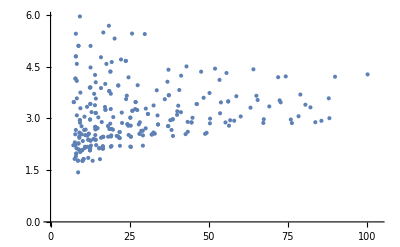

```mathematica
statsX=Select[stats,#[[1]]>=50&];
ListPlot[{Sqrt[#[[1]]],#[[2]]}&/@statsX]
```

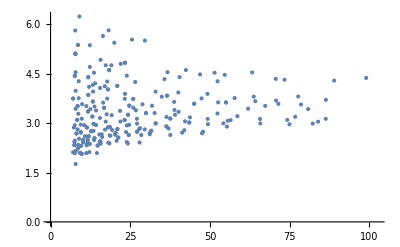

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{Sqrt[#[[3]]],#[[4]]}&/@statsX]
```

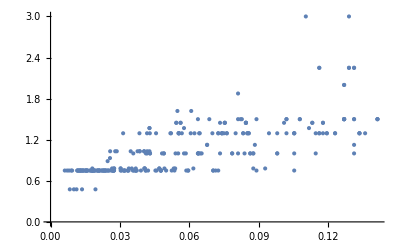

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{1/Sqrt[#[[3]]],#[[5]]}&/@statsX]
```

## Sanity Check

```mathematica
(* Usage example *)
ADUpToLevel[2,24][[1;;5]]
ADUpToLevel[3,16][[1;;5]]
ADUpToLevel[4,15][[1;;5]]
```

{{0,17990},{0.47546,26},{0.75,1302},{0.7804,610},{0.82568,2}}

{{0,2544},{0.83324,8},{0.85942,72},{1.03884,4},{1.1305,4}}

{{0,2051},{0.88412,10},{1.27864,6},{1.29666,16},{1.31934,6}}

```mathematica
(* Sanity check *)
NumAllStatesUpToLevel[2,24]
NumAllStatesUpToLevel[3,16]
NumAllStatesUpToLevel[4,15]
```

17990

2544

2051